```mathematica
ClearAll["Global`*"]

q=Table[RandomReal[{-1,1}],{q,0,Pi/2,.1}];
Positions[q_,r_]:=Module[{p,X},
X=Table[{0,0},{i,1,Length[q]}];
Do[
p=q[[n-1]];
X[[n]]=X[[n-1]]+r*{Cos[p],Sin[p]};
,{n,2,Length[q],1}];
Return[X];
]
(*ListPlot[Positions[Table[q[i],{i,0,5,1}],1],Joined->True]*)
Column@Simplify@Positions[Table[Q[i],{i,0,5,1}],1]

func[x_]:=(c1*x+c2*x^2)*Sin[k*x-ω*t]

(*ある角度を設定した場合の座標,y座標み正しくすすまないはず*)
tab=Table[i,{i,0,Pi/100,Pi/100/10}];
k=1;
ω=1;
c1=1;
c2=1;
t=0;
tab=Table[Q[i],{i,0,10,1}];
```

{0,0}
{Cos[Q[0]],Sin[Q[0]]}
{Cos[Q[0]]+Cos[Q[1]],Sin[Q[0]]+Sin[Q[1]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]+Sin[Q[4]]}

```mathematica
tab
Column@Table[{Cos[tab[[i]]],func[Cos[tab[[i]]]]},{i,1,Length[tab]}]
```

{Q[0],Q[1],Q[2],Q[3],Q[4],Q[5],Q[6],Q[7],Q[8],Q[9],Q[10]}

{Cos[Q[0]],(Cos[Q[0]]+Cos[Q[0]]^2) Sin[Cos[Q[0]]]}
{Cos[Q[1]],(Cos[Q[1]]+Cos[Q[1]]^2) Sin[Cos[Q[1]]]}
{Cos[Q[2]],(Cos[Q[2]]+Cos[Q[2]]^2) Sin[Cos[Q[2]]]}
{Cos[Q[3]],(Cos[Q[3]]+Cos[Q[3]]^2) Sin[Cos[Q[3]]]}
{Cos[Q[4]],(Cos[Q[4]]+Cos[Q[4]]^2) Sin[Cos[Q[4]]]}
{Cos[Q[5]],(Cos[Q[5]]+Cos[Q[5]]^2) Sin[Cos[Q[5]]]}
{Cos[Q[6]],(Cos[Q[6]]+Cos[Q[6]]^2) Sin[Cos[Q[6]]]}
{Cos[Q[7]],(Cos[Q[7]]+Cos[Q[7]]^2) Sin[Cos[Q[7]]]}
{Cos[Q[8]],(Cos[Q[8]]+Cos[Q[8]]^2) Sin[Cos[Q[8]]]}
{Cos[Q[9]],(Cos[Q[9]]+Cos[Q[9]]^2) Sin[Cos[Q[9]]]}
{Cos[Q[10]],(Cos[Q[10]]+Cos[Q[10]]^2) Sin[Cos[Q[10]]]}

```mathematica
Column@Positions[tab,1]
analitic=Table[{Cos[tab[[i]]],func[Cos[tab[[i]]]]},{i,1,Length[tab]}];
numeric=Positions[tab,1];

eq=Flatten[analitic-numeric]

Solve[eq==Table[0,{i,1,Length[tab]}],Q]
```

{0,0}
{Cos[Q[0]],Sin[Q[0]]}
{Cos[Q[0]]+Cos[Q[1]],Sin[Q[0]]+Sin[Q[1]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]+Sin[Q[4]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]]+Cos[Q[5]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]+Sin[Q[4]]+Sin[Q[5]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]]+Cos[Q[5]]+Cos[Q[6]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]+Sin[Q[4]]+Sin[Q[5]]+Sin[Q[6]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]]+Cos[Q[5]]+Cos[Q[6]]+Cos[Q[7]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]+Sin[Q[4]]+Sin[Q[5]]+Sin[Q[6]]+Sin[Q[7]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]]+Cos[Q[5]]+Cos[Q[6]]+Cos[Q[7]]+Cos[Q[8]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]+Sin[Q[4]]+Sin[Q[5]]+Sin[Q[6]]+Sin[Q[7]]+Sin[Q[8]]}
{Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]]+Cos[Q[5]]+Cos[Q[6]]+Cos[Q[7]]+Cos[Q[8]]+Cos[Q[9]],Sin[Q[0]]+Sin[Q[1]]+Sin[Q[2]]+Sin[Q[3]]+Sin[Q[4]]+Sin[Q[5]]+Sin[Q[6]]+Sin[Q[7]]+Sin[Q[8]]+Sin[Q[9]]}

{Cos[Q[0]],(Cos[Q[0]]+Cos[Q[0]]^2) Sin[Cos[Q[0]]],-Cos[Q[0]]+Cos[Q[1]],(Cos[Q[1]]+Cos[Q[1]]^2) Sin[Cos[Q[1]]]-Sin[Q[0]],-Cos[Q[0]]-Cos[Q[1]]+Cos[Q[2]],(Cos[Q[2]]+Cos[Q[2]]^2) Sin[Cos[Q[2]]]-Sin[Q[0]]-Sin[Q[1]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]+Cos[Q[3]],(Cos[Q[3]]+Cos[Q[3]]^2) Sin[Cos[Q[3]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]-Cos[Q[3]]+Cos[Q[4]],(Cos[Q[4]]+Cos[Q[4]]^2) Sin[Cos[Q[4]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]]-Sin[Q[3]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]-Cos[Q[3]]-Cos[Q[4]]+Cos[Q[5]],(Cos[Q[5]]+Cos[Q[5]]^2) Sin[Cos[Q[5]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]]-Sin[Q[3]]-Sin[Q[4]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]-Cos[Q[3]]-Cos[Q[4]]-Cos[Q[5]]+Cos[Q[6]],(Cos[Q[6]]+Cos[Q[6]]^2) Sin[Cos[Q[6]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]]-Sin[Q[3]]-Sin[Q[4]]-Sin[Q[5]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]-Cos[Q[3]]-Cos[Q[4]]-Cos[Q[5]]-Cos[Q[6]]+Cos[Q[7]],(Cos[Q[7]]+Cos[Q[7]]^2) Sin[Cos[Q[7]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]]-Sin[Q[3]]-Sin[Q[4]]-Sin[Q[5]]-Sin[Q[6]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]-Cos[Q[3]]-Cos[Q[4]]-Cos[Q[5]]-Cos[Q[6]]-Cos[Q[7]]+Cos[Q[8]],(Cos[Q[8]]+Cos[Q[8]]^2) Sin[Cos[Q[8]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]]-Sin[Q[3]]-Sin[Q[4]]-Sin[Q[5]]-Sin[Q[6]]-Sin[Q[7]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]-Cos[Q[3]]-Cos[Q[4]]-Cos[Q[5]]-Cos[Q[6]]-Cos[Q[7]]-Cos[Q[8]]+Cos[Q[9]],(Cos[Q[9]]+Cos[Q[9]]^2) Sin[Cos[Q[9]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]]-Sin[Q[3]]-Sin[Q[4]]-Sin[Q[5]]-Sin[Q[6]]-Sin[Q[7]]-Sin[Q[8]],-Cos[Q[0]]-Cos[Q[1]]-Cos[Q[2]]-Cos[Q[3]]-Cos[Q[4]]-Cos[Q[5]]-Cos[Q[6]]-Cos[Q[7]]-Cos[Q[8]]-Cos[Q[9]]+Cos[Q[10]],(Cos[Q[10]]+Cos[Q[10]]^2) Sin[Cos[Q[10]]]-Sin[Q[0]]-Sin[Q[1]]-Sin[Q[2]]-Sin[Q[3]]-Sin[Q[4]]-Sin[Q[5]]-Sin[Q[6]]-Sin[Q[7]]-Sin[Q[8]]-Sin[Q[9]]}

{}

```mathematica
ListPlot[Cos[#1]&@@@Positions[tab,1],Joined->True]

Column@(#1&@@@Positions[Table[Q[i],{i,0,5,1}],1])
```

-Graphics-

0
Cos[Q[0]]
Cos[Q[0]]+Cos[Q[1]]
Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]
Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]
Cos[Q[0]]+Cos[Q[1]]+Cos[Q[2]]+Cos[Q[3]]+Cos[Q[4]]

```mathematica
Inverse[{{1,0,0},{1,1,0},{1,1,1}}]
```

{{1,0,0},{-1,1,0},{0,-1,1}}

```mathematica
TableTheta[{x0_,y0_},r_,t_,n_]:=Module[{},
{x[0],y[0]}={x0,y0};
q=Table[0,{i,1,n,1}];
Do[
q[[i]]=Re@Theta[{x[i-1],y[i-1]},r,t];
{x[i],y[i]}={Cos[q[[i]]],Sin[q[[i]]]};
,{i,1,n,1}];
Return[q];
]
```

```mathematica
Servo[q_,r_]:=Module[{xy},
xy=Table[{0,0},{i,1,Length[q],1}];
Do[
xy[[i]]=xy[[i-1]]+r*{Cos[q[[i-1]]],Sin[q[[i-1]]]};
,{i,2,Length[q],1}];
Return[xy];
]
```

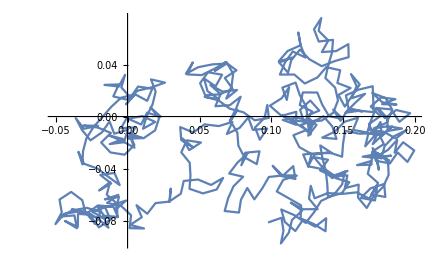

```mathematica
ListPlot[Servo[TableTheta[{0,0},.01,0,500],.01],Joined->True]
```

```mathematica
(*2021/07/19*)
```

```mathematica
ClearAll["Global`*"]
```

(0.0909091 Cos[q[0]] | 0.0909091 Sin[q[0]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]]+0.0909091 Cos[q[5]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]+0.0909091 Sin[q[5]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]]+0.0909091 Cos[q[5]]+0.0909091 Cos[q[6]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]+0.0909091 Sin[q[5]]+0.0909091 Sin[q[6]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]]+0.0909091 Cos[q[5]]+0.0909091 Cos[q[6]]+0.0909091 Cos[q[7]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]+0.0909091 Sin[q[5]]+0.0909091 Sin[q[6]]+0.0909091 Sin[q[7]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]]+0.0909091 Cos[q[5]]+0.0909091 Cos[q[6]]+0.0909091 Cos[q[7]]+0.0909091 Cos[q[8]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]+0.0909091 Sin[q[5]]+0.0909091 Sin[q[6]]+0.0909091 Sin[q[7]]+0.0909091 Sin[q[8]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]]+0.0909091 Cos[q[5]]+0.0909091 Cos[q[6]]+0.0909091 Cos[q[7]]+0.0909091 Cos[q[8]]+0.0909091 Cos[q[9]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]+0.0909091 Sin[q[5]]+0.0909091 Sin[q[6]]+0.0909091 Sin[q[7]]+0.0909091 Sin[q[8]]+0.0909091 Sin[q[9]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]]+0.0909091 Cos[q[5]]+0.0909091 Cos[q[6]]+0.0909091 Cos[q[7]]+0.0909091 Cos[q[8]]+0.0909091 Cos[q[9]]+0.0909091 Cos[q[10]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]+0.0909091 Sin[q[5]]+0.0909091 Sin[q[6]]+0.0909091 Sin[q[7]]+0.0909091 Sin[q[8]]+0.0909091 Sin[q[9]]+0.0909091 Sin[q[10]]
0.0909091 Cos[q[0]]+0.0909091 Cos[q[1]]+0.0909091 Cos[q[2]]+0.0909091 Cos[q[3]]+0.0909091 Cos[q[4]]+0.0909091 Cos[q[5]]+0.0909091 Cos[q[6]]+0.0909091 Cos[q[7]]+0.0909091 Cos[q[8]]+0.0909091 Cos[q[9]]+0.0909091 Cos[q[10]]+0.0909091 Cos[q[11]] | 0.0909091 Sin[q[0]]+0.0909091 Sin[q[1]]+0.0909091 Sin[q[2]]+0.0909091 Sin[q[3]]+0.0909091 Sin[q[4]]+0.0909091 Sin[q[5]]+0.0909091 Sin[q[6]]+0.0909091 Sin[q[7]]+0.0909091 Sin[q[8]]+0.0909091 Sin[q[9]]+0.0909091 Sin[q[10]]+0.0909091 Sin[q[11]])

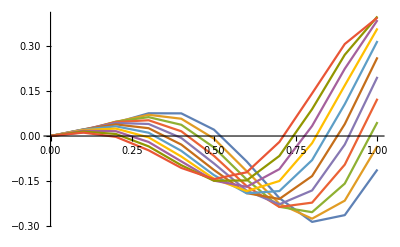

```mathematica
c1=.2;
L=1.;
c2=.2;
w=2.;
k=6.;
t=1;

n=12;

X[0]={0,0};
r=L/(n-1);
Do[Q[i]=r*{Cos[q[i]],Sin[q[i]]},{i,0,n,1}]
Do[
X[i+1]=X[i]+Q[i];
,{i,0,n,1}]
Table[X[i],{i,1,n,1}]//MatrixForm

y[x_,t_]:=(c1*x/L+c2*(x/L)^2)*Sin[k*(x/L)+w*t]
ListPlot[Table[Table[{x,y[x,t]},{x,0,L,.1}],{t,0,1,.1}],Joined->True]
```

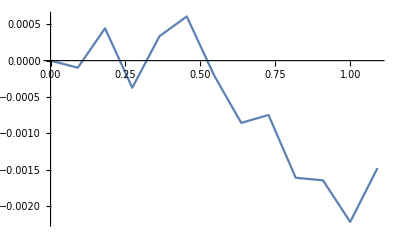

```mathematica
Do[sol[i]=RandomReal[{-0.01,.01}],{i,0,n-1,1}];
tmp=Table[q[i]->sol[i],{i,0,n-1,1}];
ListPlot[Table[X[i],{i,0,n,1}]/.tmp,Joined->True]
```

```mathematica
inits=Table[RandomReal[{-0.01,.01}],{i,1,n,1}];
Clear[t];
tmp=(Table[(#2-y[#1,t])^2&@@X[i],{i,1,n,1}]);
f[t_]=tmp;
tmp=Transpose@ParallelTable[D[f[t],q[i]],{i,0,n-1,1}];
DfDq[t_]=tmp;
get[t_]:=Module[{sol,tmp,dq},
sol=inits;
Do[
tmp=Table[q[i]->sol[[i+1]],{i,0,n-1,1}];
dq=-Dot[Inverse[DfDq[t]/.tmp],f[t]/.tmp];
sol+=dq;
If[Norm[dq]<10^-1,Break[]];
,{i,1,20,1}];
(*inits=sol;*)
Return[sol];
]
```

```mathematica
(*t=0;
Do[
f=Table[(#2-y[#1,t])^2&@@X[i],{i,1,n,1}];
DfDq=Transpose[ParallelTable[D[f,q[n]],{n,0,n-1,1}]];
tmp=Table[q[i]->sol[i],{i,0,n-1,1}];
dq=-Re@Dot[Inverse[DfDq/.tmp],f/.tmp];
(*Print["f = ",f/.tmp];*)
Do[sol[i]+=Re@dq[[i+1]],{i,0,n-1,1}];
(*Print[Table[sol[i],{i,1,n-1,1}]];*)
If[Norm[dq]<10^-5,Break[]];
,{i,1,20,1}];
*)
t=0;
Manipulate[
s=get[t];
tmp=Table[q[i]->s[[i+1]],{i,0,n-1,1}];
Table[Re@X[i],{i,1,n,1}]/.tmp;
Show[
ListPlot[Table[Re@X[i],{i,0,n,1}]/.tmp],
ListPlot[Table[{x,y[x,t]},{x,0,L,.01}],Joined->True],
PlotRange->{{0,2},{-1.,1.}},
PlotLabel->{s/Pi*180//MatrixForm}
]
,{t,0,10,.01}]
```